```mathematica
Get["C:\\Users\\mihap\\Downloads\\tocke.m"]
```

```mathematica
montecarlo[n_]:=Module[{pi,krog,kvadrat},
krog=tocke[n][[1]];
kvadrat=tocke[n][[2]];
tocke[n];
(*Print[krog];
Print[kvadrat];*);
Print[Length[krog]];
pi=4.0 (Length[krog]/n);
Print["približek pi pri ",n," točkah: ", pi];

(*izris*);
PlotNot=ListPlot[krog,PlotStyle->{PointSize[0.01],Red},PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesLabel->{"x","y"}];
PlotZun=ListPlot[kvadrat,PlotStyle->{PointSize[0.01],Green},PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesLabel->{"x","y"}];
scatterPlotAll=Show[PlotNot,PlotZun,Graphics[{Circle[{0,0},1,{0,Pi/2}]}]]];
```

7806

približek pi pri 10000 točkah: 3.1224

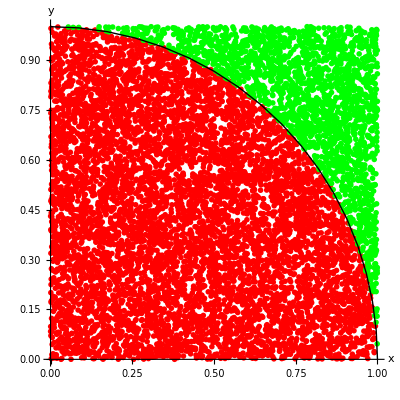

```mathematica
montecarlo[10000]
```

```mathematica
tocke[10]
```

{{0.19564,0.678155},{0.258233,0.964101},{0.395237,0.888902},{0.203793,0.427208},{0.150654,0.338236},{0.727604,0.420753},{0.148833,0.16597},{0.148314,0.948999}}

{{0.995168,0.386659},{0.97706,0.778156}}

```mathematica
tocke[10]
```

{{0.380476,-0.563391},{0.235248,0.0321284},{0.615402,0.195231},{0.365022,-0.0910778},{0.0299557,-0.52471},{-0.236242,-0.301726},{0.351728,-0.392153}}

{{-0.965155,0.531054},{-0.961963,0.674547},{0.950287,0.89105}}

7